phy1610: hw5rootmin

{{0.,{{-0.215017,0.150218}}},{0.0208333,{{-0.245855,0.151878}}},{0.0416667,{{-0.277038,0.153594}}},{0.0625,{{-0.308577,0.155371}}},{0.0833333,{{-0.340485,0.157214}}},{0.104167,{{-0.372777,0.159132},{-0.199484,0.448183}}},{0.125,{{-0.40547,0.161133},{-0.291224,0.450434}}},{0.145833,{{-0.43858,0.163228},{-0.383387,0.452335}}},{0.166667,{{-0.472128,0.165428},{-0.47591,0.453974}}},{0.1875,{{-0.506138,0.167751},{-0.568746,0.455407}}},{0.208333,{{-0.540636,0.170216},{-0.661857,0.456676}}},{0.229167,{{-0.575654,0.172851},{-0.755213,0.457812}}},{0.25,{{-0.611231,0.175691},{-0.848789,0.458837}}},{0.270833,{{-0.647412,0.178789},{-0.942565,0.459769}}},{0.291667,{{-0.684259,0.182219},{-1.03652,0.460623}}},{0.3125,{{-0.721849,0.186103},{-1.13065,0.461407}}},{0.333333,{{-0.760296,0.190659},{-1.22493,0.462133}}},{0.354167,{{-0.799778,0.196362},{-1.31935,0.462807}}},{0.375,{{-1.4139,0.463436}}},{0.395833,{{-1.50858,0.464024}}},{0.416667,{{-1.60338,0.464576}}},{0.4375,{{-1.69828,0.465096}}},{0.458333,{{-1.79329,0.465586}}},{0.479167,{{-1.8884,0.46605}}},{0.5,{{-1.98359,0.46649}}}}

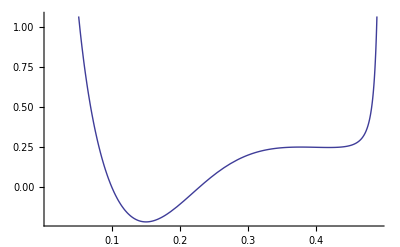
{-Graphics-,{{-0.215017,0.150218}}}

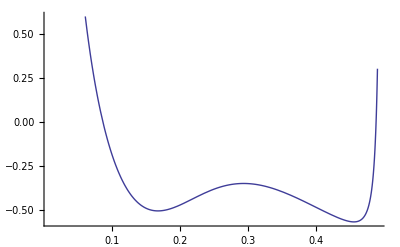
{-Graphics-,{{-0.506138,0.167751},{-0.568746,0.455407}}}

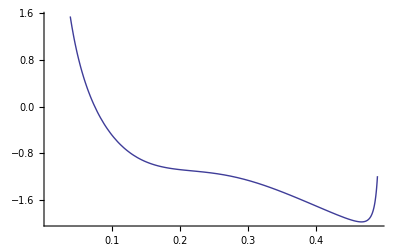
{-Graphics-,{{-1.98359,0.46649}}}

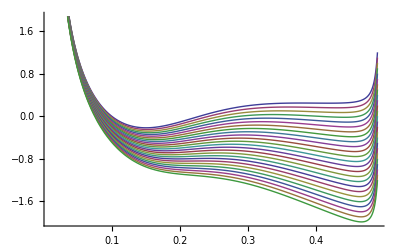

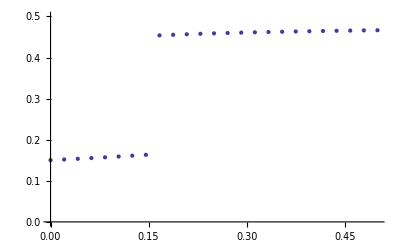

```mathematica
ClearAll[ a, b, c, d, f, g, m, e, x ]

a=1(*J energy scale*) ;
b=0.1(*m length scale*) ;
c=100(*N/m spring constant*) ;
d=0.5(*m maximum spring extension*) ;
f=2500 (*stiffness at maximum extension*) ;
g=9.8(*m/s 2 gravitational accelleration.*) ;

(*E[x, m]*)
e := a ( b/#1 + d^2/f/(#1-d)^2 - Exp[ -c(#1-b)^2/2/a]) - #2 g #1 & ;
massValues = 0.5/(25-1) (Range[25] -1) ;
fMinOne[ m_, r1_, r2_ ] :=  Minimize[ {e[x, m], {x > r1, x< r2}},x] ;

fMinAll[m_] := Module[{min1, min2, x1, x2},
min1 = fMinOne[ m, 0, d/2 ] ;
min2 = fMinOne[ m, d/2,d ] ;
x1 = x /. (min1 //Last) ;
x2 = x /. (min2 //Last) ;
r = {} ;
If [ x1 ≠ d/2, AppendTo[r, min1], ] ;
If [ x2 ≠ d/2, AppendTo[r, min2], ] ;
{#// First, (x /.(#//Last))} &/@ r
] ;

fMinGlob[m_] := Module[{min, xx},
min = fMinOne[ m, 0, d ] ;

{min// First, (x /.(min//Last))}
] ;


eps := 0.01 ;
plotAndShowMins[m_] := Module[{r},
r = fMinAll[ m ] ;
{
Plot[ e[x,m] , {x, eps, d-eps}],
r
}
] ;


{massValues, fMinAll[ # ] &/@ massValues} // Transpose

plotAndShowMins[ massValues // First] 
plotAndShowMins[ massValues[[10]]] 
plotAndShowMins[ massValues // Last] 
Plot[ Evaluate[e[x,#] &/@ massValues], {x, eps, d-eps}]

globalMins = fMinGlob[#] &/@ massValues ;

(*These are the values of the energy function at the min points for each mass value: *)
(*(#// First )&/@globalMins*) 

(*These are the x-positions where the global minimums are found at for each mass value: *)
minLocations  =(#// Last )&/@globalMins ;

(* As pairs {m, x_glmin} :*)
globalMinLocations ={massValues, minLocations} // Transpose ;

ListPlot[ globalMinLocations, PlotRange -> {Automatic,{0,0.5}} ]
```